```mathematica
(* Folowing Mathematica Tutorials *)
(* ---#2 Introduction--- *)
(* part a: Syntax of the Mathematica Language*)

"Symbol:"  α
FullForm[!x + x!]


FullForm[α - β * γ]
"shows mathematica's order of operations. I prefer to use lots of parentheses instead"
"hello world" <> "escapekey-f-escape is ϕ, and so on for greek letters"
"escape key gives a special symbol. surrounding certain kewords with this gives mathematical symbols like ∫ , and ⅆ or ∞"

FullForm[{x,y,z}]

"function calls:"
"low priority"
FullForm[3+2x //f]
"high priority"
FullForm[3 + f@(2x)]
```

Symbol: α

Not[Plus[x,Factorial[x]]]

Plus[\[Alpha],Times[-1,\[Beta],\[Gamma]]]

shows mathematica's order of operations. I prefer to use lots of parentheses instead

hello worldescapekey-f-escape is ϕ, and so on for greek letters

escape key gives a special symbol. surrounding certain kewords with this gives mathematical symbols like ∫ , and ⅆ or ∞

List[x,y,z]

function calls:

low priority

f[Plus[3,Times[2,x]]]

high priority

Plus[3,f[Times[2,x]]]

```mathematica
(* May 21, continuing in order to catch up*)

(* part a continued *)
```

```mathematica
∫k[x]ⅆx //FullForm
```

Integrate[k[x],x]

```mathematica
D[(Cos[x])^(1/2), x]
```

-Sin[x]/(2 √Cos[x])

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
(* part b *)
```

```mathematica
(* Head function is like type() in python *)
Head[f[x]]
Head[x+y]
Head[45]
Head[y]
```

f

Plus

Integer

Symbol

```mathematica
Head[{3,4,5,6,7}]
```

List

```mathematica
(* lists are containers *)
List[4,5,6]
```

{4,5,6}

```mathematica
(* part c *)

(* grouping "()" and creating list "{}" *)
mylist = {(x+2)^2,4,5}
```

{(2+x)^2,4,5}

```mathematica
(* calling function "[]" or refering to list index "[[ ]]" *)

mylist[[0]] (* indexing starts at 1 for mathematica *)
mylist[[1]]
mylist[[3]]
Integrate[mylist[[1]] ,{x,0,4}]
```

List

(2+x)^2

5

208/3

```mathematica
(* part d *)
```

```mathematica
1 + 2/3

(1 + 2) /3
```

5/3

1

```mathematica
{1,2,b,√(9+y), "hi there"}
```

{1,2,b,√(9+y),hi there}

```mathematica
Range[8]
Sin[2]
N[Sin[2]] (* gives numerical evaluation *)
```

{1,2,3,4,5,6,7,8}

Sin[2]

0.909297

```mathematica
ll = Range[10]^2 (* element-wise *)
ll[[3]]
```

{1,4,9,16,25,36,49,64,81,100}

9

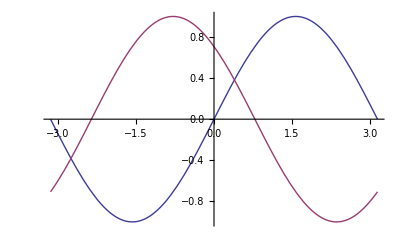

```mathematica
Plot[{Sin[x],Cos[x+(Pi/4)]},{x,-Pi,Pi}]
```

```mathematica
(* ------#3 Symbolic Analysis---- ---*)
```

```mathematica
3x - x + 2
```

2+2 x

```mathematica
x^2 -x -4x^2
```

-x-3 x^2

```mathematica
(* Expand of Factor polynomials symbolically *)
(x + 2y + 1)(x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
Expand[%] (* % sign calls previous output *)
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[1 + x]^4
```

(1+x)^2

```mathematica
(* part b *)
```

```mathematica
1 + 2x /. x->3
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
Expand[%]
```

7-5 y+y^2

```mathematica
x->3+y
```

x→3+y

```mathematica
x^2 - 9 /.%
```

-9+(3+y)^2

```mathematica
x^2+y^2/.{x->r Cos[θ],y-> r Sin[θ]}
```

r^2 Cos[θ]^2+r^2 Sin[θ]^2

```mathematica
Factor[%]
```

r^2 (Cos[θ]^2+Sin[θ]^2)

```mathematica
x=3
```

3

```mathematica
(* now x will be replaced by 3 in all expressions *)
```

```mathematica
(* to remove the value held by x: *)
x=.
```

```mathematica
x
```

x

```mathematica
x^3 + 7x
```

7 x+x^3

```mathematica
%/.x->3
```

48

```mathematica
x
```

x

```mathematica
(* the expression valule replacement notation affects only the
single expression. It does not give x a permanent vaule *)
```

```mathematica
(* part c : transforming algebraic expressions *)
(* I already tested Factor, Expand, and % *)
```

```mathematica
(* part d : smplifying algebraic expressions*)
```

```mathematica
Simplify[x^2 + 2x +1]
```

(1+x)^2

```mathematica
f = 1/(x^4 -1)
Integrate[f,x]
```

1/(-1+x^4)

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
(*Differentiate to get back original expression, but need to also simplify *)

D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
FullSimplify[r^2(Cos[θ]^2 + Sin[θ]^2)] (* something I tried previously *)
```

r^2

```mathematica
FullSimplify[Gamma[x]Gamma[x-1]]
```

Gamma[-1+x] Gamma[x]

```mathematica
(* -------#4 Calculus ------ *)

(* part a *)
```

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^n,{x,3}] (* 3rd derivative*)
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[((x y)^n)+ψ,x,{y,2}]
(* take the first derivative with resect to x,  and then take two derivatives with respect to y *)
```

(-2+n) (-1+n) n x^2 y (x y)^(-3+n)+2 (-1+n) n x (x y)^(-2+n)

```mathematica
D[x^2 + y[x]^2,x]
```

2 x+2 y[x] y'[x]

```mathematica
(* outputs a prime notation derivative *)
```

```mathematica
D[x^2 + y^2,x,NonConstants->{y}]
```

2 x+2 y D[y,x,NonConstants→{y}]

```mathematica
(* vector calculus *)

f = Exp[x^2 + y^2] (* function from R^2 to R *)

D[f,{{x,y},1}]  (* gradient *)

D[f,{{x,y},2}] (* Hessian matrix (2x2 in this case *)
```

ⅇ^(x^2+y^2)

{2 ⅇ^(x^2+y^2) x,2 ⅇ^(x^2+y^2) y}

{{2 ⅇ^(x^2+y^2)+4 ⅇ^(x^2+y^2) x^2,4 ⅇ^(x^2+y^2) x y},{4 ⅇ^(x^2+y^2) x y,2 ⅇ^(x^2+y^2)+4 ⅇ^(x^2+y^2) y^2}}

```mathematica
F = {f/.{x->u+v,y->2u-v},f/.{x->u,y->v}} (* function from R^2 to R^2 (reusing f) *)

D[F,{{u,v},1}]  (* Jacobian (determinate not yet taken) *)
```

{ⅇ^((2 u-v)^2+(u+v)^2),ⅇ^(u^2+v^2)}

{{ⅇ^((2 u-v)^2+(u+v)^2) (4 (2 u-v)+2 (u+v)),ⅇ^((2 u-v)^2+(u+v)^2) (-2 (2 u-v)+2 (u+v))},{2 ⅇ^(u^2+v^2) u,2 ⅇ^(u^2+v^2) v}}

```mathematica
(* part b *)
```

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[1/(x^4 - a^4),x]
```

-ArcTan[x/a]/(2 a^3)+Log[a-x]/(4 a^3)-Log[a+x]/(4 a^3)

```mathematica
Integrate[x^x,x]
```

∫x^x ⅆx

```mathematica
f = x^2 + y^2
```

x^2+y^2

```mathematica
(* multiple indefinite integral : *)
Integrate[f,x,y]
```

1/3 x y (x^2+y^2)

```mathematica
(* multiple definite integral : *)
Integrate[f,{x,0,4},{y,0,4}]
```

512/3

```mathematica
Integrate[x^x,{x,0,2}]
```

∫_0^2 x^x ⅆx

```mathematica
N[%]  (* can still numerically integrate *)
```

2.83388

```mathematica
(* part c *)

Integrate[x^2,x]
```

x^3/3

```mathematica
D[%+c,x] (* any symbol that is not dependent on the variable of differentiation is assumed constant wrt the variable*)
```

x^2

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
D[%,x]
```

-1/(2 (1-x))-1/(2 (1+x))

```mathematica
Simplify[%]
```

1/(-1+x^2)

```mathematica
(* Integrate also treats undefined symbols as independent of the variable of integration. *)
Integrate[a x^2,x]
```

(a x^3)/3

```mathematica
(* part d *)
DSolve[y'[x] + y[x] == 1 ,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
y[x] + 2y'[x] + y[0]/.% (* does not replace y'[x] or y[0] *)
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
DSolve[y'[x] + y[x] == 1 ,y,x]
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

```mathematica
y[x] + 2y'[x] + y[0]/.%
```

{2+C[1]-ⅇ^-x C[1]}

```mathematica
(* ------ # 5 Plotting ------ *)

(* part a *)
```

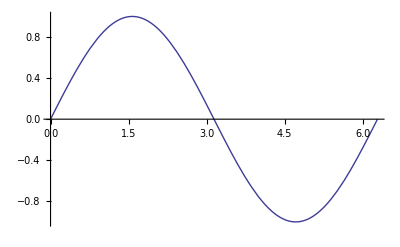

```mathematica
Plot[Sin[x],{x,0,2 π}]
```

{1.55106,-1.2265,5.75368,1.52563,1.68875,5.41039,2.22195,7.93863,11.0897,12.4636,7.71022,13.6997,11.6441,11.894,17.8659,16.1057,19.7159,19.8283,15.4244,17.5974,23.5536}

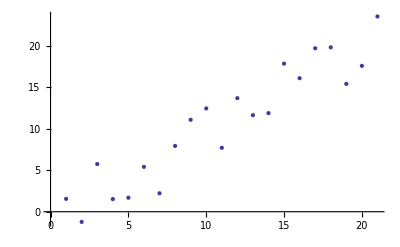

```mathematica
datapoints = Table[x+RandomReal[{-4,4}],{x,0,20}]
ListPlot[datapoints]
```

```mathematica
ListLinePlot[datapoints]
```

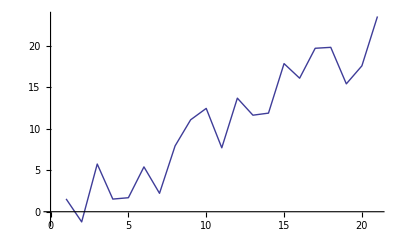

```mathematica
Plot3D[Sin[x]+Cos[y],{x,0,10},{y,0,10}]
```

-Graphics3D-

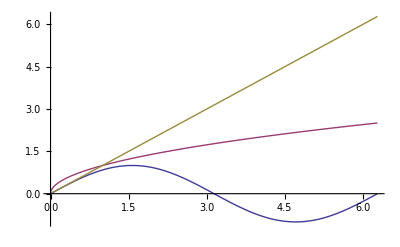

```mathematica
Plot[{Sin[x],Sqrt[x],x},{x,0,2 π}]
```

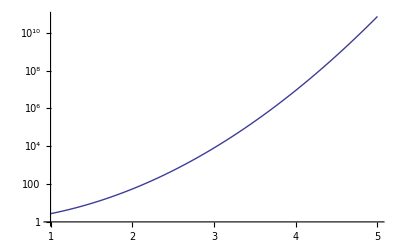

```mathematica
LogPlot[E^x^2,{x,1,5}]
```

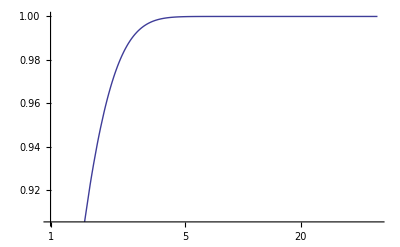

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}]
```

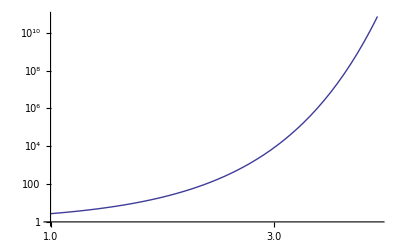

```mathematica
LogLogPlot[E^x^2,{x,1,5}]
```

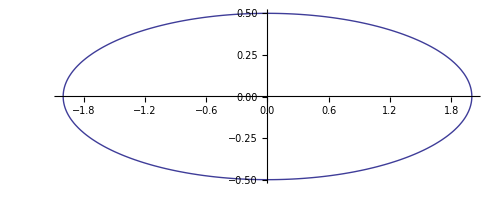

```mathematica
ParametricPlot[{2Sin[t],0.5Cos[t]},{t,0,2Pi}]
```

```mathematica
ParametricPlot3D[{5Cos[t],5Sin[t],t+Sin[t]},{t,0,4 Pi}]
```

-Graphics3D-

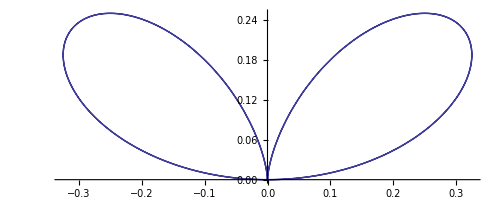

```mathematica
PolarPlot[Cos[t]^2 Sin[t],{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t], Log[r^2 ]},{t,0,2 Pi},{r,.1,4}]
```

-Graphics3D-

```mathematica
(* ------ # 6 Manipulate ------*)
```

```mathematica
Table[n,{n,1,100}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Manipulate[n,{n,1,100,0.5}]
```

```mathematica
Manipulate[Plot[Sin[Pi ω x],{x,0,2 Pi}],{ω,1,16,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Sin[Pi n1 x] + Sin[Pi n2 x],{x,0,4Pi},PlotRange->2],{n1,1,20,Appearance->"Labeled"},{n2,1,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,20,1}]
```